```mathematica
MRtab=Import[StringJoin[NotebookDirectory[],"Mann2015_Tables5_6_7.txt"],"Data"][[68;;All]];
MRtab=Table[ToExpression[StringSplit[StringJoin[Characters[First[MRtab[[i]]]][[74;;101]]]," "]],{i,1,Length[MRtab]}];
MRtab=Select[MRtab,#[[1]]>0&&#[[3]]>0&];
MRtab=Table[{MRtab[[i,3]],MRtab[[i,4]],MRtab[[i,1]],MRtab[[i,2]]},{i,1,Length[MRtab]}];
```

```mathematica
MRtab=Select[MRtab,#[[1]]>0.12&];
```

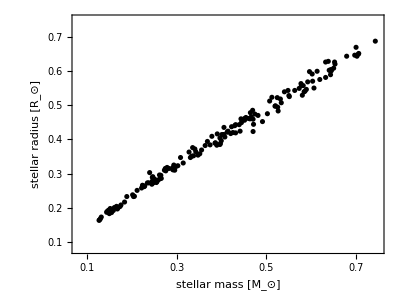

```mathematica
xticks=Table[{x,ToString[x]},{x,0.1,0.7,0.1}];
xticks2=Table[{x,""},{x,0.1,0.7,0.1}];
Show[ListPlot[MRtab[[All,{1,3}]],PlotRange->{{0.08,0.75},{0.08,0.75}},AspectRatio->0.75,Frame->True,FrameLabel->{"stellar mass [M_⊙]","stellar radius [R_⊙]"},FrameTicks->{{xticks,xticks2},{xticks,xticks2}},FrameStyle->Black,BaseStyle->{FontFamily->"CMU Serif",Black,FontSize->24},PlotStyle->Black]]
```